High quality beam produced by tightly focused laser driven wakefield accelerators

Original authors of paper: Jia Wang, Ming Zeng, Dazhang Li, Xiaoning Wang, and Jie Gao
e-print: https://arxiv.org/abs/2304.10730 (2023)
Notebook: Óscar Amaro, September 2023 @ GoLP-EPP

## Equation 5: bubble radius

```mathematica
Clear[Fpr,F,α,Ω,γavg,ωp,k, c,κ2,res,r,W,W0]
α=Ω γavg;
ωp=k c;
κ2=ωp^2 me/α;
res=Solve[-κ2 r==(me c^2 a0^2 W0^2 r)/(W^4 γavg)Exp[-2 r^2/W^2],r][[3,1,2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(ⅈ W √Log[-(k^2 W^4)/(a0^2 W0^2 Ω)])/(√2)

## Figure 7 and 8

3.92699×10^-12 a0 npcm √(-1+(2.76893×10^12 a0)/(√npcm (1.029+a0/100-4.96032×10^-14 npcm-0.0215424 W0)^2 W0)) (1.029+a0/100-4.96032×10^-14 npcm-0.0215424 W0)^2 W0^2 𝒞

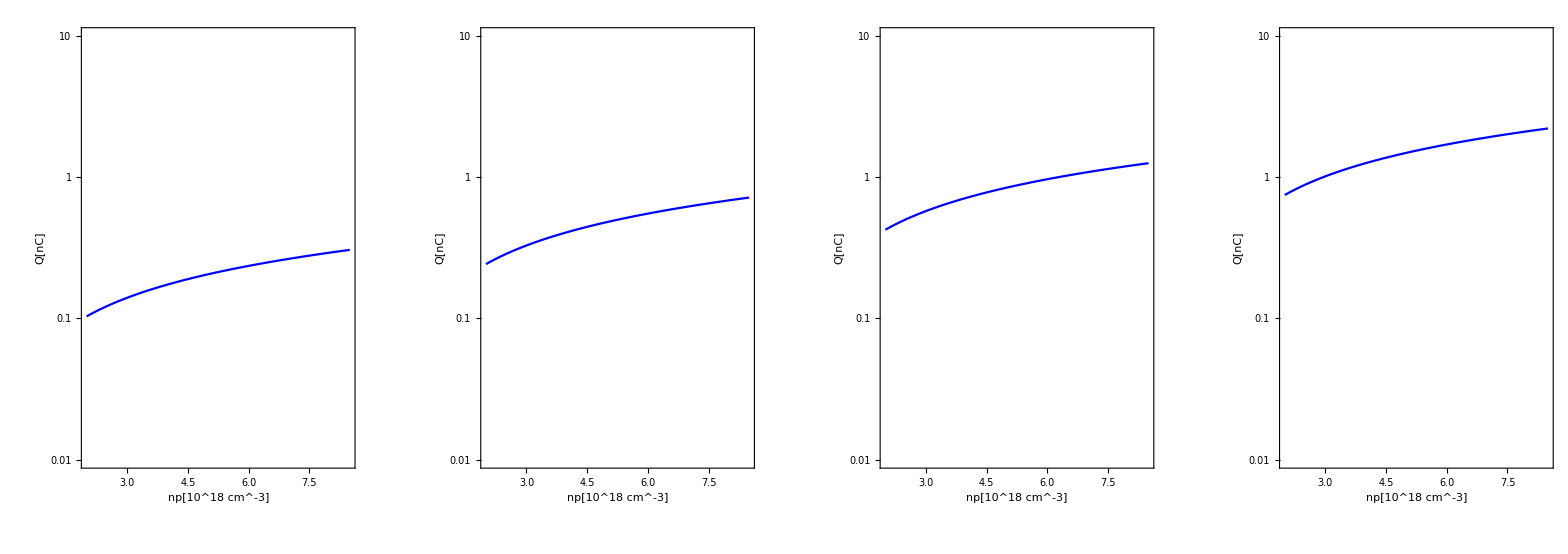

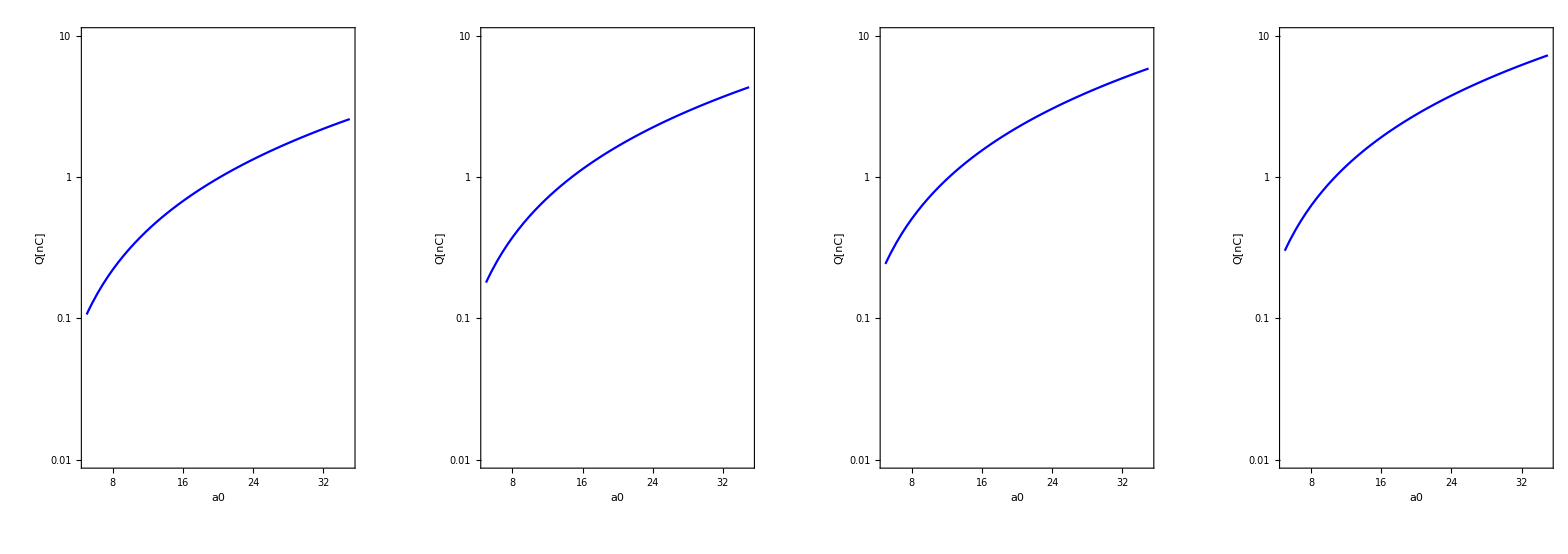

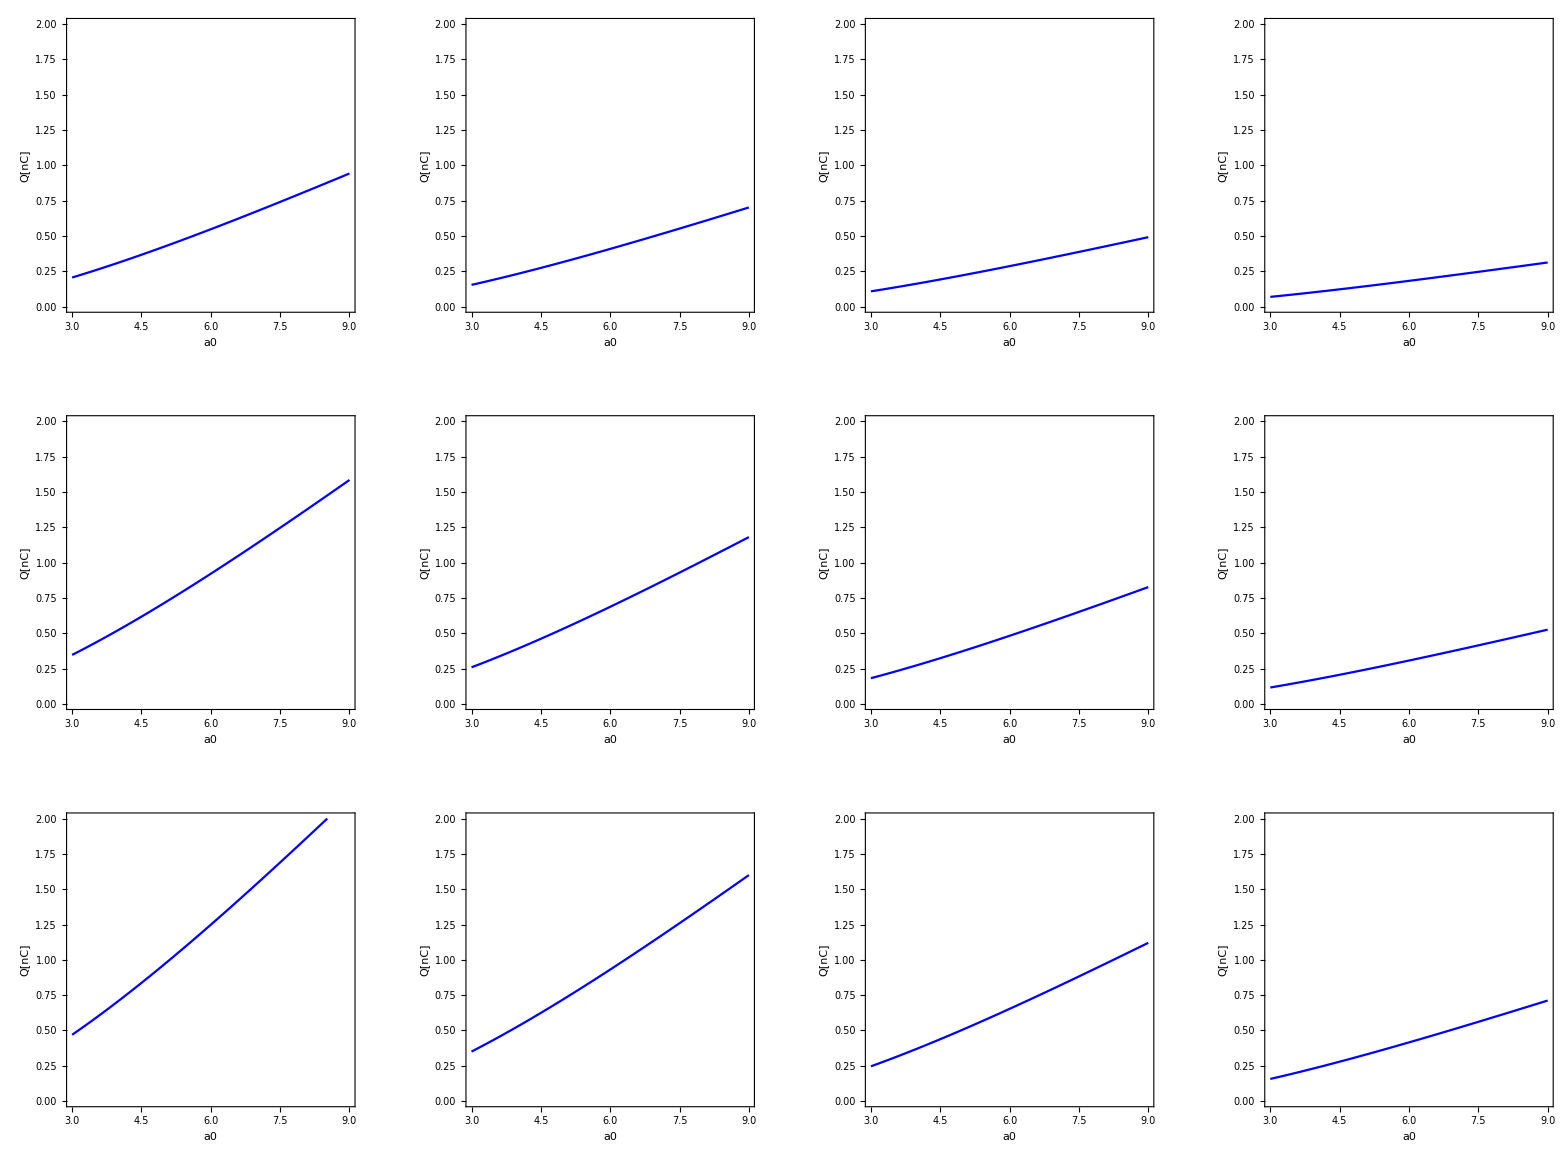

```mathematica
Clear[Linj,zRe,Ω,a0,kp,W0,Γ,Q,𝒞,λ,kp,ωp,c,e,ϵ0,me,npcm,a0lst,npcmlst]

me=9.1 10^-31;(*[Kg]*)
c=3 10^8;(*[m/s]*)
ωp=Sqrt[(np e^2)/(me ϵ0)];(*[1/s]*)
kp=ωp/c;(*[1/m]*)
e=1.6 10^-19;(*[C]*)
ϵ0=8.854 10^-12;(*[F/m]*)

λ=0.8;(*[μm] see §IV *)
Ω=2;(* see §IV *)
zRe=π W0^2 Γ^2/λ; (* after eq 2 *)
Linj = zRe Sqrt[Exp[-1](√Ω a0)/(Γ^2 kp W0)-1];(*eq 7*)
Γ=-np/20.16+a0/100-W0/46.42+1.029;(*eq 9 *)
Q = 𝒞 Linj np a0(*eq 8 *)

𝒞=8 10^-8;(* this value, although not expllicit in the text, seems to reproduce results of figures 7 and 8 *)
np= 10^-12 npcm;

(* Figure 7 *)
a0lst={4.9,8.45,12,16.97};
GraphicsRow[Table[LogPlot[10^9 Q/.{W0->5,a0->a0lst[[i]]},{npcm,2,8.5},AspectRatio->1.5,ImageSize->150,Frame->True,PlotRange->{10^-2,10^1},PlotStyle->Blue,FrameLabel->{"np[10^18 cm^-3]","Q[nC]"}],{i,1,4}]]

npcmlst={2,4,6,8};
GraphicsRow[Table[LogPlot[10^9 Q/.{W0->5,npcm->npcmlst[[i]]},{a0,5,35},AspectRatio->1.5,ImageSize->150,Frame->True,PlotRange->{10^-2,10^1},PlotStyle->Blue,FrameLabel->{"a0","Q[nC]"}],{i,1,4}]]

(* Figure 8 *)
a0lst={12,10,8,6};
npcmlst={2,4,6};
GraphicsGrid[Table[Plot[10^9 Q/.{a0->a0lst[[i]],npcm->npcmlst[[j]]},{W0,3,9},AspectRatio->1,ImageSize->150,Frame->True,PlotRange->{0,2},PlotStyle->Blue,FrameLabel->{"a0","Q[nC]"}],{j,1,3},{i,1,4}]
]
```